Lets fix the coupling as m:

```mathematica
beta=1;
```

Load the package (including examples):

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

Possible values for the argument of DataG:

```mathematica
Keys[test]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,104,triangle with two exits,15,16,17,18,20,21,22,Jamaratv9,23,19,27,Braess split,Braess congest,New Braess,Big Braess split,Big Braess congest,Paper example,Grid1020,Grid0303}

#### First example

```mathematica
t="Paper example";
D1=DataG[t]/.{I1->20,I2->10,S1->3,S2->2,S3->5,S4->4};
D1=DataG[t]/.{I1->20,I2->10,S1->0,S2->0,S3->0,S4->0};
d1=Data2Equations[D1];
D1
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,20},{3,10}},Exit Vertices and Terminal Costs→{{2,0},{4,0}},Switching Costs→{{1,2,3,0},{3,2,1,0},{2,3,4,0},{4,3,2,0}}|>

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
AbsoluteTiming[CriticalCongestionSolver[d1];]
```

InitRules

Simplifying SC...

SSC done!

Solving some balances: jt5+jt7==jt1&&20==jt2&&jt2==jt3+jt4&&jt11+jt13==jt5+jt6&&0==jt7+jt8&&jt3+jt8==jt10+jt9&&jt16==jt11+jt12&&10==jt13+jt14&&jt14+jt9==jt15&&0==jt16&&u11==u12&&u13==u14&&u5==0&&u9==0

TripleClean...
{u2==u3&&u4==u7,jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&u12≤u1&&u2≤u5&&u3≤u5&&u14≤u4&&u14≤u7&&u8≤u9,(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(jt1==0||jt2==0)&&(jt10==0||jt13==0)&&(jt11==0||jt9==0)&&(jt12==0||jt14==0)&&(jt15==0||jt16==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0)&&jt1==0&&(jt2==0||u1-u12==0)&&(jt3==0||-u2+u3==0)&&(jt4==0||-u2+u5==0)&&(jt5==0||u2-u3==0)&&(jt6==0||-u3+u5==0)&&jt7==0&&jt8==0&&(jt9==0||-u4+u7==0)&&jt10==0&&(jt11==0||u4-u7==0)&&jt12==0&&(jt13==0||-u14+u4==0)&&(jt14==0||-u14+u7==0)&&(jt15==0||-u8+u9==0)&&jt16==0}

TripleStep 1: u2==u3&&u4==u7

TripleStep 1.5: jt1≥0&&-10+jt1+jt10+jt13+jt15-jt5≥0&&30-jt1-jt10-jt13-jt15+jt5≥0&&jt5≥0&&jt11+jt13-jt5≥0&&jt1-jt5≥0&&-jt1+jt5≥0&&-10+jt13+jt15≥0&&jt10≥0&&jt11≥0&&-jt11≥0&&jt13≥0&&10-jt13≥0&&jt15≥0&&jt1≥0&&jt11+jt13≥0&&-10+jt10+jt13+jt15≥0&&30-jt1-jt10+jt11-jt15≥0&&jt15≥0&&jt15≥0&&jt1≥0&&jt10-jt11≥0&&u11≤u1&&u2≤0&&u2≤0&&u13≤u4&&u13≤u4&&u8≤0

TripleStep 2: jt1==0&&(jt11+jt13==0||-10+jt10+jt13+jt15==0)&&jt1==0&&jt10-jt11==0&&jt1==0&&(jt10==0||jt13==0)&&(jt11==0||-10+jt13+jt15==0)&&(-jt11==0||10-jt13==0)&&(-10+jt1+jt10+jt13+jt15-jt5==0||jt5==0)&&(30-jt1-jt10-jt13-jt15+jt5==0||jt1-jt5==0)&&(jt11+jt13-jt5==0||-jt1+jt5==0)&&jt1==0&&u1-u11==0&&(-10+jt1+jt10+jt13+jt15-jt5==0||-u2+u3==0)&&(30-jt1-jt10-jt13-jt15+jt5==0||-u2==0)&&(jt5==0||u2-u3==0)&&(jt11+jt13-jt5==0||-u3==0)&&jt1-jt5==0&&-jt1+jt5==0&&(-10+jt13+jt15==0||-u4+u7==0)&&jt10==0&&(jt11==0||u4-u7==0)&&-jt11==0&&(jt13==0||-u13+u4==0)&&(10-jt13==0||-u13+u7==0)&&(jt15==0||-u8==0)

TripleStep 1: jt1==0&&jt1==0&&jt10-jt11==0&&jt1==0&&jt1==0&&u1-u11==0&&jt1-jt5==0&&-jt1+jt5==0&&jt10==0&&-jt11==0

TripleStep 1.5: -10+jt13+jt15≥0&&30-jt13-jt15≥0&&jt13≥0&&-10+jt13+jt15≥0&&jt13≥0&&10-jt13≥0&&jt15≥0&&jt13≥0&&-10+jt13+jt15≥0&&30-jt15≥0&&jt15≥0&&jt15≥0&&u1≤u1&&u2≤0&&u2≤0&&u13≤u4&&u13≤u4&&u8≤0

TripleStep 2: (jt11+jt13==0||-10+jt10+jt13+jt15==0)&&(jt10==0||jt13==0)&&(jt11==0||-10+jt13+jt15==0)&&(-jt11==0||10-jt13==0)&&(-10+jt1+jt10+jt13+jt15-jt5==0||jt5==0)&&(30-jt1-jt10-jt13-jt15+jt5==0||jt1-jt5==0)&&(jt11+jt13-jt5==0||-jt1+jt5==0)&&(30-jt1-jt10-jt13-jt15+jt5==0||-u2==0)&&(jt11+jt13-jt5==0||-u2==0)&&(jt13==0||-u13+u4==0)&&(10-jt13==0||-u13+u4==0)&&(jt15==0||-u8==0)

Preprocessing: NewSystem after first TripleClean: {True,-10+jt13+jt15≥0&&30-jt13-jt15≥0&&jt13≥0&&-10+jt13+jt15≥0&&jt13≥0&&10-jt13≥0&&jt15≥0&&jt13≥0&&-10+jt13+jt15≥0&&30-jt15≥0&&jt15≥0&&jt15≥0&&u1≤u1&&u2≤0&&u2≤0&&u13≤u4&&u13≤u4&&u8≤0,(jt11+jt13==0||-10+jt10+jt13+jt15==0)&&(jt10==0||jt13==0)&&(jt11==0||-10+jt13+jt15==0)&&(-jt11==0||10-jt13==0)&&(-10+jt1+jt10+jt13+jt15-jt5==0||jt5==0)&&(30-jt1-jt10-jt13-jt15+jt5==0||jt1-jt5==0)&&(jt11+jt13-jt5==0||-jt1+jt5==0)&&(30-jt1-jt10-jt13-jt15+jt5==0||-u2==0)&&(jt11+jt13-jt5==0||-u2==0)&&(jt13==0||-u13+u4==0)&&(10-jt13==0||-u13+u4==0)&&(jt15==0||-u8==0)}

TripleClean again (with some more equalities)...

TripleStep 1: 20-u1+u2==cpc1&&-10+jt15-u2+u4==cpc2&&jt15-u4+u8==cpc3

TripleStep 1.5: -10+jt13+jt15≥0&&30-jt13-jt15≥0&&jt13≥0&&10-jt13≥0&&jt15≥0&&30-jt15≥0&&u1≤u1&&-20+cpc1+u1≤0&&u13≤-10+cpc1+cpc2-jt15+u1&&-10+cpc1+cpc2+cpc3-2 jt15+u1≤0

TripleStep 2: (jt13==0||-10+jt13+jt15==0)&&(30-jt13-jt15==0||-u2==0)&&(jt13==0||-u2==0)&&(jt13==0||-u13+u4==0)&&(10-jt13==0||-u13+u4==0)&&(jt15==0||-u8==0)

Preprocessing: NewSystem after second TripleClean: {True,-10+jt13+jt15≥0&&30-jt13-jt15≥0&&jt13≥0&&10-jt13≥0&&jt15≥0&&30-jt15≥0&&u1≤u1&&-20+cpc1+u1≤0&&u13≤-10+cpc1+cpc2-jt15+u1&&-10+cpc1+cpc2+cpc3-2 jt15+u1≤0,(jt13==0||-10+jt13+jt15==0)&&(30-jt13-jt15==0||-u2==0)&&(jt13==0||-u2==0)&&(jt13==0||-u13+u4==0)&&(10-jt13==0||-u13+u4==0)&&(jt15==0||-u8==0)}

Preprocessing took 0.019671 seconds to terminate.

Starting Solver

Replaced: {True,jt13+jt15≥10&&jt13+jt15≤30&&jt13≥0&&jt13≤10&&jt15≥0&&jt15≤30&&u1≤u1&&u1≤20&&10+jt15+u13≤u1&&u1≤2 (5+jt15),(jt13==0||jt13+jt15==10)&&(jt13+jt15==30||u2==0)&&(jt13==0||u2==0)&&(jt13==0||u13==u4)&&(jt13==10||u13==u4)&&(jt15==0||u8==0)}

Feeding this to FinalStep:\n{True,10≤jt13+jt15≤30&&0≤jt13≤10&&0≤jt15≤30&&u1≤20&&10+jt15+u13≤u1&&2 (5+jt15)≥u1,(jt13==0||u13==u4)&&(jt13==0||u2==0)&&(jt15==0||u8==0)&&(jt13==10||u13==u4)&&(jt13==0||jt13+jt15==10)&&(jt13+jt15==30||u2==0)}

jt15==0

jt13==10

Iterative DNF convertion took 0.034516 seconds to terminate.

Reducing (each alternative) took 0.012594 seconds to terminate.

FinalStep 1: {True,True,(u13==u4&&u8==0&&jt13==0&&jt15==30&&((u4<-20&&40+u4≤u1≤20)||(u4==-20&&u1==20)))||(u2==0&&u13==u4&&jt15==0&&jt13==10&&((u4<0&&10+u4≤u1≤10)||(u4==0&&u1==10)))||(u2==0&&u13==u4&&jt13==10-jt15&&u8==0&&((u1≤10&&0≤jt15≤10&&u4≤-10-jt15+u1)||(10<u1≤20&&1/2 (-10+u1)≤jt15≤10&&u4≤-10-jt15+u1)))||(u2==0&&u8==0&&u1≤20&&10≤jt15≤30&&u4≤-10-jt15+u1&&u13==u4&&jt13==0)}

u2==0&&u13==u4&&jt13==10-jt15&&u8==0&&((u1≤10&&0≤jt15≤10&&u4≤-10-jt15+u1)||(10<u1≤20&&1/2 (-10+u1)≤jt15≤10&&u4≤-10-jt15+u1))

u1>10&&u1≤20&&2 jt13+u1≤30

u13==u4&&u8==0&&jt13==0&&jt15==30&&((u4<-20&&40+u4≤u1≤20)||(u4==-20&&u1==20))

u13<-20&&40+u13≤u1≤20

u2==0&&u13==u4&&jt15==0&&jt13==10&&((u4<0&&10+u4≤u1≤10)||(u4==0&&u1==10))

u13<0&&10+u13≤u1≤10

Iterative DNF convertion took 0.025405 seconds to terminate.

Reducing (each alternative) took 0.021877 seconds to terminate.

MFGSS: (Possibly) Multiple solutions: (u2==0.&&jt15==0.&&jt13==10.&&u1==10.&&u13==0.&&u4==0.)||(u8==0.&&jt13==0.&&20.+u4==0.&&u1==20.&&jt15==30.&&20.+u13==0.)||(u1≥10.+u4&&u2==0.&&jt15==0.&&jt13==10.&&u1≤10.&&u13==u4&&u4<0.)||(u1≥40.+u4&&u13==u4&&u8==0.&&jt13==0.&&20.+u4<0.&&u1≤20.&&jt15==30.)||(u2==0.&&jt15==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&u1==0.&&10.+u4==0.)||(u2==0.&&jt15==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&u1==10.+u4&&u4<-10.)||(u2==0.&&jt15==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&u1==10.+u4&&-10.<u4≤0.)||(u2==0.&&u13==u4&&u8==0.&&u1==0.&&jt13==0.&&jt15==10.&&20.+u4==0.)||(u2==0.&&u13==u4&&u8==0.&&jt13==0.&&jt15==10.&&u1==20.+u4&&u4<-20.)||(u2==0.&&u13==u4&&u8==0.&&jt13==0.&&jt15==10.&&u1==20.+u4&&-20.<u4≤0.)||(jt15≥10.&&u2==0.&&u13==u4&&u8==0.&&jt13==0.&&20.+u4==0.&&jt15≤30.&&u1==20.)||(jt15≥0.&&u2==0.&&u1==10.&&u13==u4&&jt13+jt15==10.&&u8==0.&&10.+u4==0.&&jt15≤10.)||(u1>10.&&jt15>5.&&u2==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&10.+jt15+u4≤u1&&u1≤20.&&jt15≤10.)||(u1>10.&&jt15>0.&&2. (5.+jt15)≥u1&&u2==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&10.+jt15+u4≤u1&&jt15≤5.)||(jt15≥10.&&u1>0.&&u2==0.&&u13==u4&&u8==0.&&jt13==0.&&20.+u4==0.&&jt15≤10.+u1&&u1<20.)||(jt15≥10.&&u1>20.+u4&&u2==0.&&u13==u4&&u8==0.&&jt13==0.&&-20.<u4≤0.&&10.+jt15+u4≤u1&&u1≤20.)||(jt15≥10.&&u1>20.+u4&&u2==0.&&u13==u4&&u8==0.&&jt13==0.&&20.+u4<0.&&u1≤40.+u4&&10.+jt15+u4≤u1)||(jt15≥10.&&u1>40.+u4&&u2==0.&&u13==u4&&u8==0.&&jt13==0.&&jt15≤30.&&20.+u4<0.&&u1≤20.)||(u1>0.&&jt15≥0.&&u2==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&10.+u4==0.&&jt15≤u1&&u1<10.)||(u1>20.+u4&&jt15≥0.&&u2==0.&&u1≤10.&&u13==u4&&jt13+jt15==10.&&u8==0.&&jt15≤10.&&10.+u4<0.)||(jt15≥0.&&u1>10.+u4&&u2==0.&&u1≤10.&&u13==u4&&jt13+jt15==10.&&u8==0.&&-10.<u4≤0.&&10.+jt15+u4≤u1)||(jt15≥0.&&u1>10.+u4&&u2==0.&&u13==u4&&jt13+jt15==10.&&u8==0.&&u1≤20.+u4&&10.+jt15+u4≤u1&&10.+u4<0.)

{{u1→20,u2→0,u4→5,u8→0,u13→5,jt13→5,jt15→5}}

Picked one value for the variable(s) {u1,u2,u4,u8,u13,jt13,jt15} {20.,0.,5.,0.,5.,5.,5.} (respectively)

{0.67031,Null}

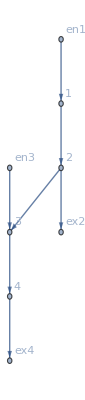

```mathematica
d1["FG"]
```

This was taking more than 25 min..... It did not have numeric values for the switching costs!

#### Second example: 3 x 3 grid

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
t="Grid0303";
(*eme=4;
ene=4;*)
D2=DataG[t];
d2=Data2Equations[D2];
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
c2=CriticalCongestionSolver[d2];
```

InitRules

Simplifying SC...

SSC done!

Solving some balances: jt11+jt9==jt1+jt2&&jt17+jt19==jt3+jt4&&400==jt5+jt6&&jt3+jt5==jt7+jt8&&jt14==jt10+jt9&&jt24+jt27+jt30==jt11+jt12&&jt12+jt7==jt13&&jt35+jt37==jt14&&jt1+jt6==jt15+jt16&&jt21+jt28+jt31==jt17+jt18&&jt40==jt19+jt20&&jt10+jt8==jt21+jt22+jt23&&jt15+jt20==jt24+jt25+jt26&&jt33+jt38==jt27+jt28+jt29&&jt43+jt45==jt30+jt31+jt32&&jt13==jt33+jt34&&jt22+jt25+jt32==jt35+jt36&&jt49+jt51==jt37+jt38&&jt16+jt18==jt39&&jt41+jt46==jt40&&jt23+jt26+jt29==jt41+jt42&&jt39==jt43+jt44&&jt47+jt52==jt45+jt46&&jt34+jt36==jt47+jt48&&jt42+jt44==jt49+jt50&&0==jt51+jt52&&u27==u28&&u25==0

TripleClean...
{u1==u3&&u2==u5&&u2==u7&&u5==u7&&u6==u9&&u11==u4&&u13==u4&&u11==u13&&u12==u8&&u15==u8&&u17==u8&&u12==u15&&u12==u17&&u15==u17&&u10==u16&&u10==u19&&u16==u19&&u14==u21&&u18==u22&&u18==u23&&u22==u23&&u20==u24,jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&u1≥u28&&u28≤u3&&u20≤u25&&u24≤u25,(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(jt1==0||jt3==0)&&(jt10==0||jt12==0)&&(jt11==0||jt8==0)&&(jt13==0||jt14==0)&&(jt15==0||jt17==0)&&(jt16==0||jt19==0)&&(jt18==0||jt20==0)&&(jt2==0||jt5==0)&&(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(jt29==0||jt32==0)&&(jt33==0||jt35==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt39==0||jt40==0)&&(jt4==0||jt6==0)&&(jt41==0||jt43==0)&&(jt42==0||jt45==0)&&(jt44==0||jt46==0)&&(jt47==0||jt49==0)&&(jt48==0||jt51==0)&&(jt50==0||jt52==0)&&(jt7==0||jt9==0)&&(jt1==0||-u1+u3==0)&&jt2==0&&(jt3==0||u1-u3==0)&&jt4==0&&(jt5==0||u1-u28==0)&&(jt6==0||-u28+u3==0)&&(jt7==0||-u2+u5==0)&&(jt8==0||-u2+u7==0)&&(jt9==0||u2-u5==0)&&(jt10==0||-u5+u7==0)&&(jt11==0||u2-u7==0)&&(jt12==0||u5-u7==0)&&(jt13==0||-u6+u9==0)&&(jt14==0||u6-u9==0)&&(jt15==0||u11-u4==0)&&(jt16==0||u13-u4==0)&&(jt17==0||-u11+u4==0)&&(jt18==0||-u11+u13==0)&&(jt19==0||-u13+u4==0)&&(jt20==0||u11-u13==0)&&(jt21==0||u12-u8==0)&&(jt22==0||u15-u8==0)&&(jt23==0||u17-u8==0)&&(jt24==0||-u12+u8==0)&&(jt25==0||-u12+u15==0)&&(jt26==0||-u12+u17==0)&&(jt27==0||-u15+u8==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u15+u17==0)&&(jt30==0||-u17+u8==0)&&(jt31==0||u12-u17==0)&&(jt32==0||u15-u17==0)&&(jt33==0||-u10+u16==0)&&(jt34==0||-u10+u19==0)&&(jt35==0||u10-u16==0)&&(jt36==0||-u16+u19==0)&&(jt37==0||u10-u19==0)&&(jt38==0||u16-u19==0)&&(jt39==0||-u14+u21==0)&&(jt40==0||u14-u21==0)&&(jt41==0||-u18+u22==0)&&(jt42==0||-u18+u23==0)&&(jt43==0||u18-u22==0)&&(jt44==0||-u22+u23==0)&&(jt45==0||u18-u23==0)&&(jt46==0||u22-u23==0)&&(jt47==0||-u20+u24==0)&&(jt48==0||-u20+u25==0)&&(jt49==0||u20-u24==0)&&(jt50==0||-u24+u25==0)&&jt51==0&&jt52==0}

TripleStep 1: u1==u3&&u2==u5&&u2==u7&&u5==u7&&u6==u9&&u11==u4&&u13==u4&&u11==u13&&u12==u8&&u15==u8&&u17==u8&&u12==u15&&u12==u17&&u15==u17&&u10==u16&&u10==u19&&u16==u19&&u14==u21&&u18==u22&&u18==u23&&u22==u23&&u20==u24

TripleStep 1.5: jt1≥0&&-jt1-jt10+jt11+jt14≥0&&-400-jt1-jt10+jt11+jt14+jt17+jt19+jt34+jt36-jt37-jt38+jt42+jt44-jt45-jt46≥0&&400+jt1+jt10-jt11-jt14-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46≥0&&400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46≥0&&-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46≥0&&-jt12+jt27+jt28+jt29+jt34-jt38≥0&&-jt10+jt17+jt18+jt22+jt23-jt28-jt31≥0&&-jt10+jt14≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt14≥0&&jt11+jt12+jt14+jt19-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt42-jt46≥0&&-jt18+jt30+jt31+jt32+jt44-jt45≥0&&jt17≥0&&jt18≥0&&jt19≥0&&-jt19+jt40≥0&&jt17+jt18-jt28-jt31≥0&&jt22≥0&&jt23≥0&&jt11+jt12-jt27-jt30≥0&&jt14-jt22-jt32+jt36-jt37≥0&&-jt23-jt29+jt40+jt42-jt46≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt27+jt28+jt29-jt38≥0&&jt34≥0&&jt14-jt37≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt40≥0&&jt40-jt46≥0&&jt42≥0&&jt30+jt31+jt32-jt45≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt45+jt46+jt51≥0&&jt34+jt36-jt45-jt46-jt51≥0&&jt37+jt38-jt51≥0&&-jt37-jt38+jt42+jt44+jt51≥0&&jt51≥0&&-jt51≥0&&-jt10+jt11+jt14≥0&&-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38≥0&&jt17+jt19≥0&&jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46≥0&&jt14≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt11+jt12≥0&&jt17+jt18+jt22+jt23-jt28-jt31≥0&&jt14≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt17+jt18≥0&&jt11+jt12+jt14-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt40+jt42-jt46≥0&&jt40≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt27+jt28+jt29≥0&&jt14+jt36-jt37≥0&&jt30+jt31+jt32≥0&&jt40+jt42-jt46≥0&&jt37+jt38≥0&&jt34+jt36≥0&&jt40≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt45+jt46≥0&&jt42+jt44≥0&&jt34+jt36-jt37-jt38+jt42+jt44-jt45-jt46≥0&&400-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46≥0&&u1≥u27&&u27≤u1&&u20≤0&&u20≤0

TripleStep 2: (-jt10+jt11+jt14==0||-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0)&&(jt17+jt19==0||jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0)&&(jt14==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt11+jt12==0||jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt14==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt17+jt18==0||jt11+jt12+jt14-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt40+jt42-jt46==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt27+jt28+jt29==0||jt14+jt36-jt37==0)&&(jt30+jt31+jt32==0||jt40+jt42-jt46==0)&&(jt37+jt38==0||jt34+jt36==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt45+jt46==0||jt42+jt44==0)&&400-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0&&(jt1==0||-400-jt1-jt10+jt11+jt14+jt17+jt19+jt34+jt36-jt37-jt38+jt42+jt44-jt45-jt46==0)&&(jt10==0||jt12==0)&&(jt11==0||-jt10+jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt27+jt28+jt29+jt34-jt38==0||jt14==0)&&(jt11+jt12+jt14+jt19-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt42-jt46==0||jt17==0)&&(-jt18+jt30+jt31+jt32+jt44-jt45==0||jt19==0)&&(jt18==0||-jt19+jt40==0)&&(-jt1-jt10+jt11+jt14==0||400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46==0)&&(jt17+jt18-jt28-jt31==0||jt11+jt12-jt27-jt30==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt14-jt22-jt32+jt36-jt37==0||jt28==0)&&(-jt23-jt29+jt40+jt42-jt46==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29-jt38==0||jt14-jt37==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt30+jt31+jt32+jt44-jt45==0||jt40==0)&&(400+jt1+jt10-jt11-jt14-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0||-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0)&&(jt40-jt46==0||jt30+jt31+jt32-jt45==0)&&(jt42==0||jt45==0)&&(jt44==0||jt46==0)&&(jt45+jt46+jt51==0||jt37+jt38-jt51==0)&&(jt34+jt36-jt45-jt46-jt51==0||jt51==0)&&(-jt37-jt38+jt42+jt44+jt51==0||-jt51==0)&&(-jt12+jt27+jt28+jt29+jt34-jt38==0||-jt10+jt14==0)&&(jt1==0||-u1+u3==0)&&-jt1-jt10+jt11+jt14==0&&(-400-jt1-jt10+jt11+jt14+jt17+jt19+jt34+jt36-jt37-jt38+jt42+jt44-jt45-jt46==0||u1-u3==0)&&400+jt1+jt10-jt11-jt14-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0&&(400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46==0||u1-u27==0)&&(-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0||-u27+u3==0)&&(-jt12+jt27+jt28+jt29+jt34-jt38==0||-u2+u5==0)&&(-jt10+jt17+jt18+jt22+jt23-jt28-jt31==0||-u2+u7==0)&&(-jt10+jt14==0||u2-u5==0)&&(jt10==0||-u5+u7==0)&&(jt11==0||u2-u7==0)&&(jt12==0||u5-u7==0)&&(jt27+jt28+jt29+jt34-jt38==0||-u6+u9==0)&&(jt14==0||u6-u9==0)&&(jt11+jt12+jt14+jt19-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt42-jt46==0||u11-u4==0)&&(-jt18+jt30+jt31+jt32+jt44-jt45==0||u13-u4==0)&&(jt17==0||-u11+u4==0)&&(jt18==0||-u11+u13==0)&&(jt19==0||-u13+u4==0)&&(-jt19+jt40==0||u11-u13==0)&&(jt17+jt18-jt28-jt31==0||u12-u8==0)&&(jt22==0||u15-u8==0)&&(jt23==0||u17-u8==0)&&(jt11+jt12-jt27-jt30==0||-u12+u8==0)&&(jt14-jt22-jt32+jt36-jt37==0||-u12+u15==0)&&(-jt23-jt29+jt40+jt42-jt46==0||-u12+u17==0)&&(jt27==0||-u15+u8==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u15+u17==0)&&(jt30==0||-u17+u8==0)&&(jt31==0||u12-u17==0)&&(jt32==0||u15-u17==0)&&(jt27+jt28+jt29-jt38==0||-u10+u16==0)&&(jt34==0||-u10+u19==0)&&(jt14-jt37==0||u10-u16==0)&&(jt36==0||-u16+u19==0)&&(jt37==0||u10-u19==0)&&(jt38==0||u16-u19==0)&&(jt30+jt31+jt32+jt44-jt45==0||-u14+u21==0)&&(jt40==0||u14-u21==0)&&(jt40-jt46==0||-u18+u22==0)&&(jt42==0||-u18+u23==0)&&(jt30+jt31+jt32-jt45==0||u18-u22==0)&&(jt44==0||-u22+u23==0)&&(jt45==0||u18-u23==0)&&(jt46==0||u22-u23==0)&&(jt45+jt46+jt51==0||-u20+u24==0)&&(jt34+jt36-jt45-jt46-jt51==0||-u20==0)&&(jt37+jt38-jt51==0||u20-u24==0)&&(-jt37-jt38+jt42+jt44+jt51==0||-u24==0)&&jt51==0&&-jt51==0

TripleStep 1: 400-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0&&-jt1-jt10+jt11+jt14==0&&400+jt1+jt10-jt11-jt14-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0&&jt51==0&&-jt51==0

TripleStep 1.5: jt1≥0&&jt17+jt19≥0&&-jt10-jt12+jt18-jt19+jt22+jt23+jt27+jt29-jt31+jt34-jt38≥0&&400+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38≥0&&-jt12+jt27+jt28+jt29+jt34-jt38≥0&&-jt10+jt17+jt18+jt22+jt23-jt28-jt31≥0&&jt1-jt11≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt1+jt10-jt11≥0&&400+jt1+jt10+jt12+jt19-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38-jt44+jt45≥0&&-jt18+jt30+jt31+jt32+jt44-jt45≥0&&jt17≥0&&jt18≥0&&jt19≥0&&-jt19+jt40≥0&&jt17+jt18-jt28-jt31≥0&&jt22≥0&&jt23≥0&&jt11+jt12-jt27-jt30≥0&&jt1+jt10-jt11-jt22-jt32+jt36-jt37≥0&&400-jt23-jt29-jt34-jt36+jt37+jt38+jt40-jt44+jt45≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt27+jt28+jt29-jt38≥0&&jt34≥0&&jt1+jt10-jt11-jt37≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt40≥0&&400-jt34-jt36+jt37+jt38+jt40-jt42-jt44+jt45≥0&&jt42≥0&&jt30+jt31+jt32-jt45≥0&&jt44≥0&&jt45≥0&&-400+jt34+jt36-jt37-jt38+jt42+jt44-jt45≥0&&-400+jt34+jt36-jt37-jt38+jt42+jt44≥0&&400+jt37+jt38-jt42-jt44≥0&&jt37+jt38≥0&&-jt37-jt38+jt42+jt44≥0&&jt1≥0&&-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38≥0&&jt17+jt19≥0&&400+jt1+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38≥0&&jt1+jt10-jt11≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt11+jt12≥0&&jt17+jt18+jt22+jt23-jt28-jt31≥0&&jt1+jt10-jt11≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt17+jt18≥0&&400+jt1+jt10+jt12-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38+jt40-jt44+jt45≥0&&jt40≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt27+jt28+jt29≥0&&jt1+jt10-jt11+jt36-jt37≥0&&jt30+jt31+jt32≥0&&400-jt34-jt36+jt37+jt38+jt40-jt44+jt45≥0&&jt37+jt38≥0&&jt34+jt36≥0&&jt40≥0&&jt30+jt31+jt32+jt44-jt45≥0&&-400+jt34+jt36-jt37-jt38+jt42+jt44≥0&&jt42+jt44≥0&&u1≥u27&&u27≤u1&&u20≤0&&u20≤0

TripleStep 2: (-jt10+jt11+jt14==0||-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0)&&(jt17+jt19==0||jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0)&&(jt14==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt11+jt12==0||jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt14==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt17+jt18==0||jt11+jt12+jt14-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt40+jt42-jt46==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt27+jt28+jt29==0||jt14+jt36-jt37==0)&&(jt30+jt31+jt32==0||jt40+jt42-jt46==0)&&(jt37+jt38==0||jt34+jt36==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt45+jt46==0||jt42+jt44==0)&&(jt1==0||-400-jt1-jt10+jt11+jt14+jt17+jt19+jt34+jt36-jt37-jt38+jt42+jt44-jt45-jt46==0)&&(jt10==0||jt12==0)&&(jt11==0||-jt10+jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt27+jt28+jt29+jt34-jt38==0||jt14==0)&&(jt11+jt12+jt14+jt19-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt42-jt46==0||jt17==0)&&(-jt18+jt30+jt31+jt32+jt44-jt45==0||jt19==0)&&(jt18==0||-jt19+jt40==0)&&(-jt1-jt10+jt11+jt14==0||400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46==0)&&(jt17+jt18-jt28-jt31==0||jt11+jt12-jt27-jt30==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt14-jt22-jt32+jt36-jt37==0||jt28==0)&&(-jt23-jt29+jt40+jt42-jt46==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29-jt38==0||jt14-jt37==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt30+jt31+jt32+jt44-jt45==0||jt40==0)&&(400+jt1+jt10-jt11-jt14-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0||-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0)&&(jt40-jt46==0||jt30+jt31+jt32-jt45==0)&&(jt42==0||jt45==0)&&(jt44==0||jt46==0)&&(jt45+jt46+jt51==0||jt37+jt38-jt51==0)&&(jt34+jt36-jt45-jt46-jt51==0||jt51==0)&&(-jt37-jt38+jt42+jt44+jt51==0||-jt51==0)&&(-jt12+jt27+jt28+jt29+jt34-jt38==0||-jt10+jt14==0)&&(400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46==0||u1-u27==0)&&(-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0||u1-u27==0)&&(jt34+jt36-jt45-jt46-jt51==0||-u20==0)&&(-jt37-jt38+jt42+jt44+jt51==0||-u20==0)

Preprocessing: NewSystem after first TripleClean: {True,jt1≥0&&jt17+jt19≥0&&-jt10-jt12+jt18-jt19+jt22+jt23+jt27+jt29-jt31+jt34-jt38≥0&&400+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38≥0&&-jt12+jt27+jt28+jt29+jt34-jt38≥0&&-jt10+jt17+jt18+jt22+jt23-jt28-jt31≥0&&jt1-jt11≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt1+jt10-jt11≥0&&400+jt1+jt10+jt12+jt19-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38-jt44+jt45≥0&&-jt18+jt30+jt31+jt32+jt44-jt45≥0&&jt17≥0&&jt18≥0&&jt19≥0&&-jt19+jt40≥0&&jt17+jt18-jt28-jt31≥0&&jt22≥0&&jt23≥0&&jt11+jt12-jt27-jt30≥0&&jt1+jt10-jt11-jt22-jt32+jt36-jt37≥0&&400-jt23-jt29-jt34-jt36+jt37+jt38+jt40-jt44+jt45≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt27+jt28+jt29-jt38≥0&&jt34≥0&&jt1+jt10-jt11-jt37≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt40≥0&&400-jt34-jt36+jt37+jt38+jt40-jt42-jt44+jt45≥0&&jt42≥0&&jt30+jt31+jt32-jt45≥0&&jt44≥0&&jt45≥0&&-400+jt34+jt36-jt37-jt38+jt42+jt44-jt45≥0&&-400+jt34+jt36-jt37-jt38+jt42+jt44≥0&&400+jt37+jt38-jt42-jt44≥0&&jt37+jt38≥0&&-jt37-jt38+jt42+jt44≥0&&jt1≥0&&-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38≥0&&jt17+jt19≥0&&400+jt1+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38≥0&&jt1+jt10-jt11≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt11+jt12≥0&&jt17+jt18+jt22+jt23-jt28-jt31≥0&&jt1+jt10-jt11≥0&&jt27+jt28+jt29+jt34-jt38≥0&&jt17+jt18≥0&&400+jt1+jt10+jt12-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38+jt40-jt44+jt45≥0&&jt40≥0&&jt30+jt31+jt32+jt44-jt45≥0&&jt27+jt28+jt29≥0&&jt1+jt10-jt11+jt36-jt37≥0&&jt30+jt31+jt32≥0&&400-jt34-jt36+jt37+jt38+jt40-jt44+jt45≥0&&jt37+jt38≥0&&jt34+jt36≥0&&jt40≥0&&jt30+jt31+jt32+jt44-jt45≥0&&-400+jt34+jt36-jt37-jt38+jt42+jt44≥0&&jt42+jt44≥0&&u1≥u27&&u27≤u1&&u20≤0&&u20≤0,(-jt10+jt11+jt14==0||-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0)&&(jt17+jt19==0||jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0)&&(jt14==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt11+jt12==0||jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt14==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt17+jt18==0||jt11+jt12+jt14-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt40+jt42-jt46==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt27+jt28+jt29==0||jt14+jt36-jt37==0)&&(jt30+jt31+jt32==0||jt40+jt42-jt46==0)&&(jt37+jt38==0||jt34+jt36==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt45+jt46==0||jt42+jt44==0)&&(jt1==0||-400-jt1-jt10+jt11+jt14+jt17+jt19+jt34+jt36-jt37-jt38+jt42+jt44-jt45-jt46==0)&&(jt10==0||jt12==0)&&(jt11==0||-jt10+jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt27+jt28+jt29+jt34-jt38==0||jt14==0)&&(jt11+jt12+jt14+jt19-jt22-jt23-jt27-jt29-jt30-jt32+jt36-jt37+jt42-jt46==0||jt17==0)&&(-jt18+jt30+jt31+jt32+jt44-jt45==0||jt19==0)&&(jt18==0||-jt19+jt40==0)&&(-jt1-jt10+jt11+jt14==0||400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46==0)&&(jt17+jt18-jt28-jt31==0||jt11+jt12-jt27-jt30==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt14-jt22-jt32+jt36-jt37==0||jt28==0)&&(-jt23-jt29+jt40+jt42-jt46==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29-jt38==0||jt14-jt37==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt30+jt31+jt32+jt44-jt45==0||jt40==0)&&(400+jt1+jt10-jt11-jt14-jt34-jt36+jt37+jt38-jt42-jt44+jt45+jt46==0||-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0)&&(jt40-jt46==0||jt30+jt31+jt32-jt45==0)&&(jt42==0||jt45==0)&&(jt44==0||jt46==0)&&(jt45+jt46+jt51==0||jt37+jt38-jt51==0)&&(jt34+jt36-jt45-jt46-jt51==0||jt51==0)&&(-jt37-jt38+jt42+jt44+jt51==0||-jt51==0)&&(-jt12+jt27+jt28+jt29+jt34-jt38==0||-jt10+jt14==0)&&(400+jt1-jt11-jt12-jt14+jt18-jt19+jt22+jt23+jt27+jt29-jt31-jt36+jt37-jt42-jt44+jt45+jt46==0||u1-u27==0)&&(-jt1+jt11+jt12+jt14-jt18+jt19-jt22-jt23-jt27-jt29+jt31+jt36-jt37+jt42+jt44-jt45-jt46==0||u1-u27==0)&&(jt34+jt36-jt45-jt46-jt51==0||-u20==0)&&(-jt37-jt38+jt42+jt44+jt51==0||-u20==0)}

TripleClean again (with some more equalities)...

TripleStep 1: -jt1-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38-u1+u5==cpc1&&400+jt1+jt10+jt12-jt17-jt18-jt22-jt23-jt27-jt29+jt31-jt34+jt38-u1+u11==cpc2&&-jt1-jt10+jt11+jt27+jt28+jt29+jt34-jt38-u5+u6==cpc3&&-jt11-jt12+jt17+jt18+jt22+jt23-jt28-jt31+u15-u5==cpc4&&-jt1-jt10+jt11+jt27+jt28+jt29+jt34-jt38+u16-u6==cpc5&&400+jt1+jt10+jt12-jt17-jt18-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38+jt40-jt44+jt45-u11+u15==cpc6&&jt30+jt31+jt32-jt40+jt44-jt45-u11+u14==cpc7&&jt1+jt10-jt11-jt27-jt28-jt29+jt36-jt37-u15+u16==cpc8&&400-jt30-jt31-jt32-jt34-jt36+jt37+jt38+jt40-jt44+jt45-u15+u22==cpc9&&jt34+jt36-jt37-jt38-u16+u20==cpc10&&jt30+jt31+jt32-jt40+jt44-jt45-u14+u22==cpc11&&400-jt34-jt36+jt37+jt38+u20-u22==cpc12

TripleStep 1.5: jt1≥0&&jt17+jt19≥0&&200+(7 cpc1)/24+cpc10/24-cpc11/12-cpc12/24-(7 cpc2)/24+cpc3/12+(5 cpc4)/24+cpc5/12-(5 cpc6)/24-cpc7/12-cpc8/24+cpc9/24+jt1-jt17-jt19≥0&&200-(7 cpc1)/24-cpc10/24+cpc11/12+cpc12/24+(7 cpc2)/24-cpc3/12-(5 cpc4)/24-cpc5/12+(5 cpc6)/24+cpc7/12+cpc8/24-cpc9/24-jt1+jt17+jt19≥0&&100+cpc1/12+cpc10/12-cpc11/24-cpc12/12-cpc2/12+(7 cpc3)/24-(5 cpc4)/24+(7 cpc5)/24-cpc6/24-cpc7/24-(5 cpc8)/24-cpc9/24+jt1+jt10-jt11-jt12≥0&&100+(5 cpc1)/24-cpc10/24-cpc11/24+cpc12/24-(5 cpc2)/24-(5 cpc3)/24+(5 cpc4)/12-(5 cpc5)/24-cpc6/6-cpc7/24+cpc8/6+cpc9/12-jt10+jt11+jt12≥0&&jt1-jt11≥0&&jt10≥0&&jt11≥0&&jt12≥0&&100+cpc1/12+cpc10/12-cpc11/24-cpc12/12-cpc2/12+(7 cpc3)/24-(5 cpc4)/24+(7 cpc5)/24-cpc6/24-cpc7/24-(5 cpc8)/24-cpc9/24+jt1+jt10-jt11≥0&&jt1+jt10-jt11≥0&&100-(5 cpc1)/24+cpc10/24-(5 cpc11)/24-cpc12/24+(5 cpc2)/24-cpc3/24-cpc4/6-cpc5/24+(5 cpc6)/12-(5 cpc7)/24+cpc8/12+cpc9/6+jt17+jt18+jt19-jt40≥0&&100-cpc1/12-cpc10/12+(7 cpc11)/24+cpc12/12+cpc2/12-cpc3/24-cpc4/24-cpc5/24-(5 cpc6)/24+(7 cpc7)/24-cpc8/24-(5 cpc9)/24-jt18+jt40≥0&&jt17≥0&&jt18≥0&&jt19≥0&&-jt19+jt40≥0&&100+(5 cpc1)/24-cpc10/24-cpc11/24+cpc12/24-(5 cpc2)/24-(5 cpc3)/24+(5 cpc4)/12-(5 cpc5)/24-cpc6/6-cpc7/24+cpc8/6+cpc9/12+jt11+jt12-jt22-jt23≥0&&jt22≥0&&jt23≥0&&jt11+jt12-jt27-jt30≥0&&100-cpc1/24+(5 cpc10)/24-cpc11/24-(5 cpc12)/24+cpc2/24-(5 cpc3)/24+cpc4/6-(5 cpc5)/24+cpc6/12-cpc7/24+(5 cpc8)/12-cpc9/6-jt22+jt27+jt28+jt29-jt32≥0&&-cpc1/6-cpc10/6-cpc11/6+cpc12/6+cpc2/6+cpc3/6-cpc4/3+cpc5/6+cpc6/3-cpc7/6-cpc8/3+cpc9/3-jt11-jt12+jt17+jt18+jt22-jt28-jt29+jt30+jt32≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&-100-(5 cpc1)/24+cpc10/24+cpc11/24-cpc12/24+(5 cpc2)/24+(5 cpc3)/24-(5 cpc4)/12+(5 cpc5)/24+cpc6/6+cpc7/24-cpc8/6-cpc9/12-jt11-jt12+jt17+jt18+jt22+jt23-jt28≥0&&jt32≥0&&100+cpc1/12+cpc10/12-cpc11/24-cpc12/12-cpc2/12+(7 cpc3)/24-(5 cpc4)/24+(7 cpc5)/24-cpc6/24-cpc7/24-(5 cpc8)/24-cpc9/24+jt1+jt10-jt11-jt34≥0&&jt34≥0&&100-cpc1/24+(5 cpc10)/24-cpc11/24-(5 cpc12)/24+cpc2/24-(5 cpc3)/24+cpc4/6-(5 cpc5)/24+cpc6/12-cpc7/24+(5 cpc8)/12-cpc9/6+jt27+jt28+jt29-jt36≥0&&jt36≥0&&-100+cpc1/24-(5 cpc10)/24+cpc11/24+(5 cpc12)/24-cpc2/24+(5 cpc3)/24-cpc4/6+(5 cpc5)/24-cpc6/12+cpc7/24-(5 cpc8)/12+cpc9/6+jt1+jt10-jt11-jt27-jt28-jt29+jt36≥0&&-100-cpc1/12-cpc10/12+cpc11/24+cpc12/12+cpc2/12-(7 cpc3)/24+(5 cpc4)/24-(7 cpc5)/24+cpc6/24+cpc7/24+(5 cpc8)/24+cpc9/24-jt1-jt10+jt11+jt27+jt28+jt29+jt34≥0&&100-cpc1/12-cpc10/12+(7 cpc11)/24+cpc12/12+cpc2/12-cpc3/24-cpc4/24-cpc5/24-(5 cpc6)/24+(7 cpc7)/24-cpc8/24-(5 cpc9)/24+jt40≥0&&jt40≥0&&-cpc1/6-cpc10/6-cpc11/6+cpc12/6+cpc2/6+cpc3/6-cpc4/3+cpc5/6+cpc6/3-cpc7/6-cpc8/3+cpc9/3-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32-jt42≥0&&jt42≥0&&100-cpc1/12-cpc10/12+(7 cpc11)/24+cpc12/12+cpc2/12-cpc3/24-cpc4/24-cpc5/24-(5 cpc6)/24+(7 cpc7)/24-cpc8/24-(5 cpc9)/24+jt40-jt44≥0&&jt44≥0&&-200-cpc1/8+cpc10/8-cpc11/4-cpc12/8+cpc2/8+cpc3/4-(3 cpc4)/8+cpc5/4+(3 cpc6)/8-cpc7/4-cpc8/8+cpc9/8-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32-jt40+jt44≥0&&cpc1/6+cpc10/6+cpc11/6-cpc12/6-cpc2/6-cpc3/6+cpc4/3-cpc5/6-cpc6/3+cpc7/6+cpc8/3-cpc9/3+jt11+jt12-jt17-jt18-jt22-jt23+jt28-jt30-jt32+jt40+jt42≥0&&-200+cpc1/24+(7 cpc10)/24-cpc11/12-(7 cpc12)/24-cpc2/24+cpc3/12-cpc4/24+cpc5/12+cpc6/24-cpc7/12+(5 cpc8)/24-(5 cpc9)/24+jt42+jt44≥0&&200-cpc1/24-(7 cpc10)/24+cpc11/12+(7 cpc12)/24+cpc2/24-cpc3/12+cpc4/24-cpc5/12-cpc6/24+cpc7/12-(5 cpc8)/24+(5 cpc9)/24+jt34+jt36-jt42-jt44≥0&&-200-cpc1/24-(7 cpc10)/24+cpc11/12+(7 cpc12)/24+cpc2/24-cpc3/12+cpc4/24-cpc5/12-cpc6/24+cpc7/12-(5 cpc8)/24+(5 cpc9)/24+jt34+jt36≥0&&200+cpc1/24+(7 cpc10)/24-cpc11/12-(7 cpc12)/24-cpc2/24+cpc3/12-cpc4/24+cpc5/12+cpc6/24-cpc7/12+(5 cpc8)/24-(5 cpc9)/24-jt34-jt36+jt42+jt44≥0&&200+(7 cpc1)/24+cpc10/24-cpc11/12-cpc12/24-(7 cpc2)/24+cpc3/12+(5 cpc4)/24+cpc5/12-(5 cpc6)/24-cpc7/12-cpc8/24+cpc9/24+jt1≥0&&200-(7 cpc1)/24-cpc10/24+cpc11/12+cpc12/24+(7 cpc2)/24-cpc3/12-(5 cpc4)/24-cpc5/12+(5 cpc6)/24+cpc7/12+cpc8/24-cpc9/24+jt17+jt19≥0&&jt11+jt12≥0&&100+(5 cpc1)/24-cpc10/24-cpc11/24+cpc12/24-(5 cpc2)/24-(5 cpc3)/24+(5 cpc4)/12-(5 cpc5)/24-cpc6/6-cpc7/24+cpc8/6+cpc9/12+jt11+jt12≥0&&jt17+jt18≥0&&100-(5 cpc1)/24+cpc10/24-(5 cpc11)/24-cpc12/24+(5 cpc2)/24-cpc3/24-cpc4/6-cpc5/24+(5 cpc6)/12-(5 cpc7)/24+cpc8/12+cpc9/6+jt17+jt18≥0&&jt27+jt28+jt29≥0&&100-cpc1/24+(5 cpc10)/24-cpc11/24-(5 cpc12)/24+cpc2/24-(5 cpc3)/24+cpc4/6-(5 cpc5)/24+cpc6/12-cpc7/24+(5 cpc8)/12-cpc9/6+jt27+jt28+jt29≥0&&-100-(5 cpc1)/24+cpc10/24+cpc11/24-cpc12/24+(5 cpc2)/24+(5 cpc3)/24-(5 cpc4)/12+(5 cpc5)/24+cpc6/6+cpc7/24-cpc8/6-cpc9/12-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32≥0&&-cpc1/6-cpc10/6-cpc11/6+cpc12/6+cpc2/6+cpc3/6-cpc4/3+cpc5/6+cpc6/3-cpc7/6-cpc8/3+cpc9/3-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32≥0&&jt34+jt36≥0&&jt42+jt44≥0&&u1≥u27&&u27≤u1&&-600+cpc1/2+cpc10/2+cpc11/4+cpc12/2+cpc2/2+cpc3/4+cpc4/4+cpc5/4+cpc6/4+cpc7/4+cpc8/4+cpc9/4+u1≤0

TripleStep 2: (jt1==0||-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0)&&(jt17+jt19==0||400+jt1+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38==0)&&(jt1+jt10-jt11==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt11+jt12==0||jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt17+jt18==0||400+jt1+jt10+jt12-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38+jt40-jt44+jt45==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt27+jt28+jt29==0||jt1+jt10-jt11+jt36-jt37==0)&&(jt30+jt31+jt32==0||400-jt34-jt36+jt37+jt38+jt40-jt44+jt45==0)&&(jt37+jt38==0||jt34+jt36==0)&&(-400+jt34+jt36-jt37-jt38+jt42+jt44==0||jt42+jt44==0)&&(jt1==0||jt17+jt19==0)&&(jt10==0||jt12==0)&&(jt11==0||-jt10+jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt27+jt28+jt29+jt34-jt38==0||jt1+jt10-jt11==0)&&(400+jt1+jt10+jt12+jt19-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38-jt44+jt45==0||jt17==0)&&(-jt18+jt30+jt31+jt32+jt44-jt45==0||jt19==0)&&(jt18==0||-jt19+jt40==0)&&(jt17+jt18-jt28-jt31==0||jt11+jt12-jt27-jt30==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt1+jt10-jt11-jt22-jt32+jt36-jt37==0||jt28==0)&&(400-jt23-jt29-jt34-jt36+jt37+jt38+jt40-jt44+jt45==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29-jt38==0||jt1+jt10-jt11-jt37==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt30+jt31+jt32+jt44-jt45==0||jt40==0)&&(400-jt34-jt36+jt37+jt38+jt40-jt42-jt44+jt45==0||jt30+jt31+jt32-jt45==0)&&(jt42==0||jt45==0)&&(jt44==0||-400+jt34+jt36-jt37-jt38+jt42+jt44-jt45==0)&&(-400+jt34+jt36-jt37-jt38+jt42+jt44==0||jt37+jt38==0)&&(-jt12+jt27+jt28+jt29+jt34-jt38==0||jt1-jt11==0)&&(-jt10-jt12+jt18-jt19+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0||u1-u27==0)&&(400+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38==0||u1-u27==0)&&(400+jt37+jt38-jt42-jt44==0||-u20==0)&&(-jt37-jt38+jt42+jt44==0||-u20==0)

Preprocessing: NewSystem after second TripleClean: {True,jt1≥0&&jt17+jt19≥0&&200+(7 cpc1)/24+cpc10/24-cpc11/12-cpc12/24-(7 cpc2)/24+cpc3/12+(5 cpc4)/24+cpc5/12-(5 cpc6)/24-cpc7/12-cpc8/24+cpc9/24+jt1-jt17-jt19≥0&&200-(7 cpc1)/24-cpc10/24+cpc11/12+cpc12/24+(7 cpc2)/24-cpc3/12-(5 cpc4)/24-cpc5/12+(5 cpc6)/24+cpc7/12+cpc8/24-cpc9/24-jt1+jt17+jt19≥0&&100+cpc1/12+cpc10/12-cpc11/24-cpc12/12-cpc2/12+(7 cpc3)/24-(5 cpc4)/24+(7 cpc5)/24-cpc6/24-cpc7/24-(5 cpc8)/24-cpc9/24+jt1+jt10-jt11-jt12≥0&&100+(5 cpc1)/24-cpc10/24-cpc11/24+cpc12/24-(5 cpc2)/24-(5 cpc3)/24+(5 cpc4)/12-(5 cpc5)/24-cpc6/6-cpc7/24+cpc8/6+cpc9/12-jt10+jt11+jt12≥0&&jt1-jt11≥0&&jt10≥0&&jt11≥0&&jt12≥0&&100+cpc1/12+cpc10/12-cpc11/24-cpc12/12-cpc2/12+(7 cpc3)/24-(5 cpc4)/24+(7 cpc5)/24-cpc6/24-cpc7/24-(5 cpc8)/24-cpc9/24+jt1+jt10-jt11≥0&&jt1+jt10-jt11≥0&&100-(5 cpc1)/24+cpc10/24-(5 cpc11)/24-cpc12/24+(5 cpc2)/24-cpc3/24-cpc4/6-cpc5/24+(5 cpc6)/12-(5 cpc7)/24+cpc8/12+cpc9/6+jt17+jt18+jt19-jt40≥0&&100-cpc1/12-cpc10/12+(7 cpc11)/24+cpc12/12+cpc2/12-cpc3/24-cpc4/24-cpc5/24-(5 cpc6)/24+(7 cpc7)/24-cpc8/24-(5 cpc9)/24-jt18+jt40≥0&&jt17≥0&&jt18≥0&&jt19≥0&&-jt19+jt40≥0&&100+(5 cpc1)/24-cpc10/24-cpc11/24+cpc12/24-(5 cpc2)/24-(5 cpc3)/24+(5 cpc4)/12-(5 cpc5)/24-cpc6/6-cpc7/24+cpc8/6+cpc9/12+jt11+jt12-jt22-jt23≥0&&jt22≥0&&jt23≥0&&jt11+jt12-jt27-jt30≥0&&100-cpc1/24+(5 cpc10)/24-cpc11/24-(5 cpc12)/24+cpc2/24-(5 cpc3)/24+cpc4/6-(5 cpc5)/24+cpc6/12-cpc7/24+(5 cpc8)/12-cpc9/6-jt22+jt27+jt28+jt29-jt32≥0&&-cpc1/6-cpc10/6-cpc11/6+cpc12/6+cpc2/6+cpc3/6-cpc4/3+cpc5/6+cpc6/3-cpc7/6-cpc8/3+cpc9/3-jt11-jt12+jt17+jt18+jt22-jt28-jt29+jt30+jt32≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&-100-(5 cpc1)/24+cpc10/24+cpc11/24-cpc12/24+(5 cpc2)/24+(5 cpc3)/24-(5 cpc4)/12+(5 cpc5)/24+cpc6/6+cpc7/24-cpc8/6-cpc9/12-jt11-jt12+jt17+jt18+jt22+jt23-jt28≥0&&jt32≥0&&100+cpc1/12+cpc10/12-cpc11/24-cpc12/12-cpc2/12+(7 cpc3)/24-(5 cpc4)/24+(7 cpc5)/24-cpc6/24-cpc7/24-(5 cpc8)/24-cpc9/24+jt1+jt10-jt11-jt34≥0&&jt34≥0&&100-cpc1/24+(5 cpc10)/24-cpc11/24-(5 cpc12)/24+cpc2/24-(5 cpc3)/24+cpc4/6-(5 cpc5)/24+cpc6/12-cpc7/24+(5 cpc8)/12-cpc9/6+jt27+jt28+jt29-jt36≥0&&jt36≥0&&-100+cpc1/24-(5 cpc10)/24+cpc11/24+(5 cpc12)/24-cpc2/24+(5 cpc3)/24-cpc4/6+(5 cpc5)/24-cpc6/12+cpc7/24-(5 cpc8)/12+cpc9/6+jt1+jt10-jt11-jt27-jt28-jt29+jt36≥0&&-100-cpc1/12-cpc10/12+cpc11/24+cpc12/12+cpc2/12-(7 cpc3)/24+(5 cpc4)/24-(7 cpc5)/24+cpc6/24+cpc7/24+(5 cpc8)/24+cpc9/24-jt1-jt10+jt11+jt27+jt28+jt29+jt34≥0&&100-cpc1/12-cpc10/12+(7 cpc11)/24+cpc12/12+cpc2/12-cpc3/24-cpc4/24-cpc5/24-(5 cpc6)/24+(7 cpc7)/24-cpc8/24-(5 cpc9)/24+jt40≥0&&jt40≥0&&-cpc1/6-cpc10/6-cpc11/6+cpc12/6+cpc2/6+cpc3/6-cpc4/3+cpc5/6+cpc6/3-cpc7/6-cpc8/3+cpc9/3-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32-jt42≥0&&jt42≥0&&100-cpc1/12-cpc10/12+(7 cpc11)/24+cpc12/12+cpc2/12-cpc3/24-cpc4/24-cpc5/24-(5 cpc6)/24+(7 cpc7)/24-cpc8/24-(5 cpc9)/24+jt40-jt44≥0&&jt44≥0&&-200-cpc1/8+cpc10/8-cpc11/4-cpc12/8+cpc2/8+cpc3/4-(3 cpc4)/8+cpc5/4+(3 cpc6)/8-cpc7/4-cpc8/8+cpc9/8-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32-jt40+jt44≥0&&cpc1/6+cpc10/6+cpc11/6-cpc12/6-cpc2/6-cpc3/6+cpc4/3-cpc5/6-cpc6/3+cpc7/6+cpc8/3-cpc9/3+jt11+jt12-jt17-jt18-jt22-jt23+jt28-jt30-jt32+jt40+jt42≥0&&-200+cpc1/24+(7 cpc10)/24-cpc11/12-(7 cpc12)/24-cpc2/24+cpc3/12-cpc4/24+cpc5/12+cpc6/24-cpc7/12+(5 cpc8)/24-(5 cpc9)/24+jt42+jt44≥0&&200-cpc1/24-(7 cpc10)/24+cpc11/12+(7 cpc12)/24+cpc2/24-cpc3/12+cpc4/24-cpc5/12-cpc6/24+cpc7/12-(5 cpc8)/24+(5 cpc9)/24+jt34+jt36-jt42-jt44≥0&&-200-cpc1/24-(7 cpc10)/24+cpc11/12+(7 cpc12)/24+cpc2/24-cpc3/12+cpc4/24-cpc5/12-cpc6/24+cpc7/12-(5 cpc8)/24+(5 cpc9)/24+jt34+jt36≥0&&200+cpc1/24+(7 cpc10)/24-cpc11/12-(7 cpc12)/24-cpc2/24+cpc3/12-cpc4/24+cpc5/12+cpc6/24-cpc7/12+(5 cpc8)/24-(5 cpc9)/24-jt34-jt36+jt42+jt44≥0&&200+(7 cpc1)/24+cpc10/24-cpc11/12-cpc12/24-(7 cpc2)/24+cpc3/12+(5 cpc4)/24+cpc5/12-(5 cpc6)/24-cpc7/12-cpc8/24+cpc9/24+jt1≥0&&200-(7 cpc1)/24-cpc10/24+cpc11/12+cpc12/24+(7 cpc2)/24-cpc3/12-(5 cpc4)/24-cpc5/12+(5 cpc6)/24+cpc7/12+cpc8/24-cpc9/24+jt17+jt19≥0&&jt11+jt12≥0&&100+(5 cpc1)/24-cpc10/24-cpc11/24+cpc12/24-(5 cpc2)/24-(5 cpc3)/24+(5 cpc4)/12-(5 cpc5)/24-cpc6/6-cpc7/24+cpc8/6+cpc9/12+jt11+jt12≥0&&jt17+jt18≥0&&100-(5 cpc1)/24+cpc10/24-(5 cpc11)/24-cpc12/24+(5 cpc2)/24-cpc3/24-cpc4/6-cpc5/24+(5 cpc6)/12-(5 cpc7)/24+cpc8/12+cpc9/6+jt17+jt18≥0&&jt27+jt28+jt29≥0&&100-cpc1/24+(5 cpc10)/24-cpc11/24-(5 cpc12)/24+cpc2/24-(5 cpc3)/24+cpc4/6-(5 cpc5)/24+cpc6/12-cpc7/24+(5 cpc8)/12-cpc9/6+jt27+jt28+jt29≥0&&-100-(5 cpc1)/24+cpc10/24+cpc11/24-cpc12/24+(5 cpc2)/24+(5 cpc3)/24-(5 cpc4)/12+(5 cpc5)/24+cpc6/6+cpc7/24-cpc8/6-cpc9/12-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32≥0&&-cpc1/6-cpc10/6-cpc11/6+cpc12/6+cpc2/6+cpc3/6-cpc4/3+cpc5/6+cpc6/3-cpc7/6-cpc8/3+cpc9/3-jt11-jt12+jt17+jt18+jt22+jt23-jt28+jt30+jt32≥0&&jt34+jt36≥0&&jt42+jt44≥0&&u1≥u27&&u27≤u1&&-600+cpc1/2+cpc10/2+cpc11/4+cpc12/2+cpc2/2+cpc3/4+cpc4/4+cpc5/4+cpc6/4+cpc7/4+cpc8/4+cpc9/4+u1≤0,(jt1==0||-jt10-jt12+jt17+jt18+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0)&&(jt17+jt19==0||400+jt1+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38==0)&&(jt1+jt10-jt11==0||jt27+jt28+jt29+jt34-jt38==0)&&(jt11+jt12==0||jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt17+jt18==0||400+jt1+jt10+jt12-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38+jt40-jt44+jt45==0)&&(jt40==0||jt30+jt31+jt32+jt44-jt45==0)&&(jt27+jt28+jt29==0||jt1+jt10-jt11+jt36-jt37==0)&&(jt30+jt31+jt32==0||400-jt34-jt36+jt37+jt38+jt40-jt44+jt45==0)&&(jt37+jt38==0||jt34+jt36==0)&&(-400+jt34+jt36-jt37-jt38+jt42+jt44==0||jt42+jt44==0)&&(jt1==0||jt17+jt19==0)&&(jt10==0||jt12==0)&&(jt11==0||-jt10+jt17+jt18+jt22+jt23-jt28-jt31==0)&&(jt27+jt28+jt29+jt34-jt38==0||jt1+jt10-jt11==0)&&(400+jt1+jt10+jt12+jt19-jt22-jt23-jt27-jt29-jt30-jt32-jt34+jt38-jt44+jt45==0||jt17==0)&&(-jt18+jt30+jt31+jt32+jt44-jt45==0||jt19==0)&&(jt18==0||-jt19+jt40==0)&&(jt17+jt18-jt28-jt31==0||jt11+jt12-jt27-jt30==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt1+jt10-jt11-jt22-jt32+jt36-jt37==0||jt28==0)&&(400-jt23-jt29-jt34-jt36+jt37+jt38+jt40-jt44+jt45==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29-jt38==0||jt1+jt10-jt11-jt37==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt30+jt31+jt32+jt44-jt45==0||jt40==0)&&(400-jt34-jt36+jt37+jt38+jt40-jt42-jt44+jt45==0||jt30+jt31+jt32-jt45==0)&&(jt42==0||jt45==0)&&(jt44==0||-400+jt34+jt36-jt37-jt38+jt42+jt44-jt45==0)&&(-400+jt34+jt36-jt37-jt38+jt42+jt44==0||jt37+jt38==0)&&(-jt12+jt27+jt28+jt29+jt34-jt38==0||jt1-jt11==0)&&(-jt10-jt12+jt18-jt19+jt22+jt23+jt27+jt29-jt31+jt34-jt38==0||u1-u27==0)&&(400+jt10+jt12-jt18+jt19-jt22-jt23-jt27-jt29+jt31-jt34+jt38==0||u1-u27==0)&&(400+jt37+jt38-jt42-jt44==0||-u20==0)&&(-jt37-jt38+jt42+jt44==0||-u20==0)}

Preprocessing took 0.467051 seconds to terminate.

Starting Solver

Replaced: {True,jt1≥0&&jt17+jt19≥0&&4800+24 jt1≥24 jt17+24 jt19&&4800+24 jt17+24 jt19≥24 jt1&&2400+24 jt1+24 jt10≥24 jt11+24 jt12&&2400+24 jt11+24 jt12≥24 jt10&&jt1≥jt11&&jt10≥0&&jt11≥0&&jt12≥0&&2400+24 jt1+24 jt10≥24 jt11&&jt1+jt10≥jt11&&2400+24 jt17+24 jt18+24 jt19≥24 jt40&&2400+24 jt40≥24 jt18&&jt17≥0&&jt18≥0&&jt19≥0&&jt40≥jt19&&2400+24 jt11+24 jt12≥24 jt22+24 jt23&&jt22≥0&&jt23≥0&&jt11+jt12≥jt27+jt30&&2400+24 jt27+24 jt28+24 jt29≥24 jt22+24 jt32&&6 jt17+6 jt18+6 jt22+6 jt30+6 jt32≥6 jt11+6 jt12+6 jt28+6 jt29&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&24 jt17+24 jt18+24 jt22+24 jt23≥2400+24 jt11+24 jt12+24 jt28&&jt32≥0&&2400+24 jt1+24 jt10≥24 jt11+24 jt34&&jt34≥0&&2400+24 jt27+24 jt28+24 jt29≥24 jt36&&jt36≥0&&24 jt1+24 jt10+24 jt36≥2400+24 jt11+24 jt27+24 jt28+24 jt29&&24 jt11+24 jt27+24 jt28+24 jt29+24 jt34≥2400+24 jt1+24 jt10&&2400+24 jt40≥0&&jt40≥0&&6 jt17+6 jt18+6 jt22+6 jt23+6 jt30+6 jt32≥6 jt11+6 jt12+6 jt28+6 jt42&&jt42≥0&&2400+24 jt40≥24 jt44&&jt44≥0&&8 jt17+8 jt18+8 jt22+8 jt23+8 jt30+8 jt32+8 jt44≥1600+8 jt11+8 jt12+8 jt28+8 jt40&&6 jt11+6 jt12+6 jt28+6 jt40+6 jt42≥6 jt17+6 jt18+6 jt22+6 jt23+6 jt30+6 jt32&&24 jt42+24 jt44≥4800&&4800+24 jt34+24 jt36≥24 jt42+24 jt44&&24 jt34+24 jt36≥4800&&4800+24 jt42+24 jt44≥24 jt34+24 jt36&&4800+24 jt1≥0&&4800+24 jt17+24 jt19≥0&&jt11+jt12≥0&&2400+24 jt11+24 jt12≥0&&jt17+jt18≥0&&2400+24 jt17+24 jt18≥0&&jt27+jt28+jt29≥0&&2400+24 jt27+24 jt28+24 jt29≥0&&24 jt17+24 jt18+24 jt22+24 jt23+24 jt30+24 jt32≥2400+24 jt11+24 jt12+24 jt28&&6 jt17+6 jt18+6 jt22+6 jt23+6 jt30+6 jt32≥6 jt11+6 jt12+6 jt28&&jt34+jt36≥0&&jt42+jt44≥0&&u1≥u27&&u27≤u1&&4 u1≤2400,(jt1==0||jt10+jt12+jt31+jt38==jt17+jt18+jt22+jt23+jt27+jt29+jt34)&&(jt17+jt19==0||400+jt1+jt10+jt12+jt19+jt31+jt38==jt18+jt22+jt23+jt27+jt29+jt34)&&(jt1+jt10==jt11||jt27+jt28+jt29+jt34==jt38)&&(jt11+jt12==0||jt17+jt18+jt22+jt23==jt28+jt31)&&(jt17+jt18==0||400+jt1+jt10+jt12+jt38+jt40+jt45==jt22+jt23+jt27+jt29+jt30+jt32+jt34+jt44)&&(jt40==0||jt30+jt31+jt32+jt44==jt45)&&(jt27+jt28+jt29==0||jt1+jt10+jt36==jt11+jt37)&&(jt30+jt31+jt32==0||jt34+jt36+jt44==400+jt37+jt38+jt40+jt45)&&(jt37+jt38==0||jt34+jt36==0)&&(jt34+jt36+jt42+jt44==400+jt37+jt38||jt42+jt44==0)&&(jt1==0||jt17+jt19==0)&&(jt10==0||jt12==0)&&(jt11==0||jt10+jt28+jt31==jt17+jt18+jt22+jt23)&&(jt27+jt28+jt29+jt34==jt38||jt1+jt10==jt11)&&(400+jt1+jt10+jt12+jt19+jt38+jt45==jt22+jt23+jt27+jt29+jt30+jt32+jt34+jt44||jt17==0)&&(jt18+jt45==jt30+jt31+jt32+jt44||jt19==0)&&(jt18==0||jt19==jt40)&&(jt17+jt18==jt28+jt31||jt11+jt12==jt27+jt30)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt1+jt10+jt36==jt11+jt22+jt32+jt37||jt28==0)&&(jt23+jt29+jt34+jt36+jt44==400+jt37+jt38+jt40+jt45||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29==jt38||jt1+jt10==jt11+jt37)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt30+jt31+jt32+jt44==jt45||jt40==0)&&(jt34+jt36+jt42+jt44==400+jt37+jt38+jt40+jt45||jt30+jt31+jt32==jt45)&&(jt42==0||jt45==0)&&(jt44==0||jt34+jt36+jt42+jt44==400+jt37+jt38+jt45)&&(jt34+jt36+jt42+jt44==400+jt37+jt38||jt37+jt38==0)&&(jt12+jt38==jt27+jt28+jt29+jt34||jt1==jt11)&&(jt10+jt12+jt19+jt31+jt38==jt18+jt22+jt23+jt27+jt29+jt34||u1==u27)&&(400+jt10+jt12+jt19+jt31+jt38==jt18+jt22+jt23+jt27+jt29+jt34||u1==u27)&&(400+jt37+jt38==jt42+jt44||u20==0)&&(jt37+jt38==jt42+jt44||u20==0)}

Feeding this to FinalStep:
{True,jt1≥0&&jt17≥0&&jt19≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt18≥0&&jt40≥0&&jt22≥0&&jt23≥0&&jt27≥0&&jt30≥0&&jt28≥0&&jt29≥0&&jt32≥0&&jt34≥0&&jt36≥0&&jt42≥0&&jt44≥0&&jt17+jt19≤200+jt1&&jt1≤200+jt17+jt19&&jt11+jt12≤100+jt1+jt10&&jt10≤100+jt11+jt12&&jt11≤jt1&&jt40≤100+jt17+jt18+jt19&&jt18≤100+jt40&&jt19≤jt40&&jt22+jt23≤100+jt11+jt12&&jt27+jt30≤jt11+jt12&&jt22+jt32≤100+jt27+jt28+jt29&&jt11+jt12+jt28+jt29≤jt17+jt18+jt22+jt30+jt32&&100+jt11+jt12+jt28≤jt17+jt18+jt22+jt23&&jt11+jt34≤100+jt1+jt10&&jt36≤100+jt27+jt28+jt29&&100+jt11+jt27+jt28+jt29≤jt1+jt10+jt36&&100+jt1+jt10≤jt11+jt27+jt28+jt29+jt34&&jt11+jt12+jt28+jt42≤jt17+jt18+jt22+jt23+jt30+jt32&&jt44≤100+jt40&&200+jt11+jt12+jt28+jt40≤jt17+jt18+jt22+jt23+jt30+jt32+jt44&&jt17+jt18+jt22+jt23+jt30+jt32≤jt11+jt12+jt28+jt40+jt42&&jt42+jt44≥200&&jt42+jt44≤200+jt34+jt36&&jt34+jt36≤200+jt42+jt44&&jt34+jt36≥200&&u27≤u1&&u1≤600,(jt10==0||jt12==0)&&(jt18==0||jt19==jt40)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt29==0||jt32==0)&&(jt34==0||jt37==0)&&(jt36==0||jt38==0)&&(jt42==0||jt45==0)&&(jt1==0||jt17+jt19==0)&&(jt37+jt38==0||jt34+jt36==0)&&(jt37+jt38==jt42+jt44||u20==0)&&(jt40==0||jt30+jt31+jt32+jt44==jt45)&&(jt30+jt31+jt32+jt44==jt45||jt40==0)&&(jt1+jt10==jt11||jt27+jt28+jt29+jt34==jt38)&&(jt27+jt28+jt29+jt34==jt38||jt1+jt10==jt11)&&(jt12+jt38==jt27+jt28+jt29+jt34||jt1==jt11)&&(jt18+jt45==jt30+jt31+jt32+jt44||jt19==0)&&(jt11==0||jt10+jt28+jt31==jt17+jt18+jt22+jt23)&&(jt27+jt28+jt29==jt38||jt1+jt10==jt11+jt37)&&(jt1+jt10+jt36==jt11+jt22+jt32+jt37||jt28==0)&&(400+jt37+jt38==jt42+jt44||u20==0)&&(jt11+jt12==0||jt17+jt18+jt22+jt23==jt28+jt31)&&(jt17+jt18==jt28+jt31||jt11+jt12==jt27+jt30)&&(jt27+jt28+jt29==0||jt1+jt10+jt36==jt11+jt37)&&(jt44==0||jt34+jt36+jt42+jt44==400+jt37+jt38+jt45)&&(jt1==0||jt10+jt12+jt31+jt38==jt17+jt18+jt22+jt23+jt27+jt29+jt34)&&(jt10+jt12+jt19+jt31+jt38==jt18+jt22+jt23+jt27+jt29+jt34||u1==u27)&&(jt34+jt36+jt42+jt44==400+jt37+jt38||jt37+jt38==0)&&(jt34+jt36+jt42+jt44==400+jt37+jt38||jt42+jt44==0)&&(jt23+jt29+jt34+jt36+jt44==400+jt37+jt38+jt40+jt45||jt31==0)&&(jt30+jt31+jt32==0||jt34+jt36+jt44==400+jt37+jt38+jt40+jt45)&&(400+jt10+jt12+jt19+jt31+jt38==jt18+jt22+jt23+jt27+jt29+jt34||u1==u27)&&(jt34+jt36+jt42+jt44==400+jt37+jt38+jt40+jt45||jt30+jt31+jt32==jt45)&&(jt17+jt19==0||400+jt1+jt10+jt12+jt19+jt31+jt38==jt18+jt22+jt23+jt27+jt29+jt34)&&(400+jt1+jt10+jt12+jt19+jt38+jt45==jt22+jt23+jt27+jt29+jt30+jt32+jt34+jt44||jt17==0)&&(jt17+jt18==0||400+jt1+jt10+jt12+jt38+jt40+jt45==jt22+jt23+jt27+jt29+jt30+jt32+jt34+jt44)}

Iterative DNF convertion took 335.73 seconds to terminate.

Reducing (each alternative) took 0.15558 seconds to terminate.

FinalStep 1: {True,True,(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt32==0&&jt31==0&&jt22==0&&jt23==100&&jt34==100&&jt36==100&&jt42==100&&jt44==100)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt22==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt32==0&&jt31==0&&jt29==0&&jt27==0&&jt23==100&&jt34==100&&jt36==100&&jt42==100&&jt44==100)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt32==0&&jt31==0&&jt23==0&&jt22==100&&jt34==100&&jt36==100&&jt42==100&&jt44==100)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt22==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt32==0&&jt31==0&&jt23==100&&jt27==0&&jt29==0&&jt34==100&&jt36==100&&jt42==100&&jt44==100)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt44==100&&jt42==100&&jt36==100&&jt34==200-jt42&&jt32==100-jt34&&jt31==-100+jt34&&jt23==200-jt34&&jt22==100-jt23)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt32==0&&jt31==0&&0≤jt23≤100&&jt44==100&&jt42==100&&jt36==100&&jt34==100&&jt22==100-jt23)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt32==0&&jt31==0&&jt22==100&&jt23==0&&jt34==100&&jt36==100&&jt42==100&&jt44==100)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt31==0&&jt23==0&&jt22==100&&jt30==0&&jt32==0&&jt34==100&&jt36==100&&jt42==100&&jt44==100)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt29==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt28==0&&jt11==0&&jt27==0&&jt32==0&&jt31==0&&0≤jt23≤100&&jt44==100&&jt42==100&&jt36==100&&jt34==100&&jt22==100-jt23)||(u20==0&&u27≤600&&u1==u27&&jt45==0&&jt40==0&&jt38==0&&jt37==0&&jt30==0&&jt19==0&&jt17==0&&jt10==0&&jt1==0&&jt12==0&&jt18==0&&jt11==0&&jt27==0&&jt32==0&&jt31==0&&jt22==100&&jt23==0&&jt28==0&&jt29==0&&jt34==100&&jt36==100&&jt42==100&&jt44==100)}

Iterative DNF convertion took 0.091658 seconds to terminate.

Reducing (each alternative) took 0.00601 seconds to terminate.

MFGSS: (Possibly) Multiple solutions: (jt1==0.&&jt10==0.&&jt11==0.&&jt12==0.&&jt17==0.&&jt18==0.&&jt19==0.&&jt27==0.&&jt28==0.&&jt29==0.&&jt30==0.&&jt31==0.&&jt32==0.&&jt34==100.&&jt36==100.&&jt37==0.&&jt38==0.&&jt40==0.&&jt42==100.&&jt44==100.&&jt45==0.&&u1==u27&&u20==0.&&u27≤600.&&jt22==0.&&jt23==100.)||(jt1==0.&&jt10==0.&&jt11==0.&&jt12==0.&&jt17==0.&&jt18==0.&&jt19==0.&&jt27==0.&&jt28==0.&&jt29==0.&&jt30==0.&&jt31==0.&&jt32==0.&&jt34==100.&&jt36==100.&&jt37==0.&&jt38==0.&&jt40==0.&&jt42==100.&&jt44==100.&&jt45==0.&&u1==u27&&u20==0.&&u27≤600.&&jt22==100.&&jt23==0.)||(jt1==0.&&jt10==0.&&jt11==0.&&jt12==0.&&jt17==0.&&jt18==0.&&jt19==0.&&jt27==0.&&jt28==0.&&jt29==0.&&jt30==0.&&jt31==0.&&jt32==0.&&jt34==100.&&jt36==100.&&jt37==0.&&jt38==0.&&jt40==0.&&jt42==100.&&jt44==100.&&jt45==0.&&u1==u27&&u20==0.&&u27≤600.&&jt22+jt23==100.&&0.≤jt23&&jt23≤100.)

{}

Picked one value for the variable(s) {u1,u20,u27,jt1,jt10,jt11,jt12,jt17,jt18,jt19,jt22,jt23,jt27,jt28,jt29,jt30,jt31,jt32,jt34,jt36,jt37,jt38,jt40,jt42,jt44,jt45} {600.,0.,600.,0.,0.,0.,0.,0.,0.,0.,0.,100.,0.,0.,0.,0.,0.,0.,100.,100.,0.,0.,0.,100.,100.,0.} (respectively)

#### Third example

```mathematica
t="Jamaratv9";
D3=DataG[t];
```

#### Fourth example

```mathematica
eme
```

4

```mathematica
ene
```

ene

```mathematica
DataG["Grid1020"]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},Adjacency Matrix→SparseArray[…],Entrance Vertices and Currents→{{1,400}},Exit Vertices and Terminal Costs→{{200,0}},Switching Costs→{}|>

```mathematica
CriticalCongestionSolver[Data2Equations[DataG["Grid1020"]]]
```

$Aborted

Aborted after some hours...